## Saturation

```mathematica
S[u_,p_]:=(u/(1+(u)^p)^(1/p));
```

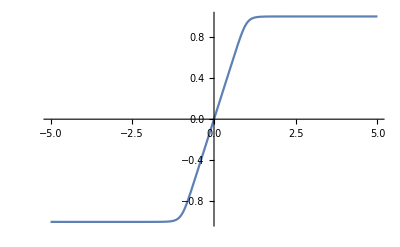

```mathematica
Plot[S[u,10],{u,-5,5}, Axes->Equal]
```

```mathematica
D[S[u,10],u]//Simplify
```

1/((1+u^10)^(11/10))

## Speeds

```mathematica
M = ({{CuT, CuT}, {r CuT, -r CuT}});
{{omegau1},{omegau2}}= Sqrt[Inverse[M].{{T},{tauuz}}]
```

{{√(T/(2 CuT)+tauuz/(2 CuT r))},{√(T/(2 CuT)-tauuz/(2 CuT r))}}

## Derivatives

### calcDesiredRotorSpeeds

```mathematica
ω1s2 = Ts/(2*KT) + τzs/(2*KT*r);
ω2s2 = Ts/(2*KT) - τzs/(2*KT*r);
```

```mathematica
ins = {Ts, τzs, KT, r};
D[ω1s2, {ins}]
D[ω2s2, {ins}]
```

{1/(2 KT),1/(2 KT r),-Ts/(2 KT^2)-τzs/(2 KT^2 r),-τzs/(2 KT r^2)}

{1/(2 KT),-1/(2 KT r),-Ts/(2 KT^2)+τzs/(2 KT^2 r),τzs/(2 KT r^2)}